```mathematica
Ω[N_,Nup_]:= N!/(Nup!*(N-Nup)!)
```

```mathematica
Ω[100,10]
```

17310309456440

```mathematica
Ω[N,Nup]
```

(N!)/((N-Nup)! Nup!)

```mathematica
S[N_,Nup_]:=N*Log[N]-Nup*Log[Nup]-(N-Nup)*Log[N-Nup]
```

```mathematica
U[N_,Nup_]:=N-2*Nup
```

```mathematica
n = Solve[U[N,Nup]==U,Nup]
```

{{Nup→(N-U)/2}}

```mathematica
n[[1]]
```

{Nup→(N-U)/2}

```mathematica
S2[N_, U_]=S[N,Nup]/.n[[1]]
```

N Log[N]-1/2 (N-U) Log[(N-U)/2]-(N+1/2 (-N+U)) Log[N+1/2 (-N+U)]

```mathematica
S2[100,-98]
```

-99 Log[99]+100 Log[100]

```mathematica
N[%]
```

5.60015

```mathematica
InvT[N_,U_]:=D[S2[N,U],U]
```

```mathematica
T[N_,U_]=InvT[N,U]^-1
```

1/(1/2 Log[(N-U)/2]-1/2 Log[N+1/2 (-N+U)])

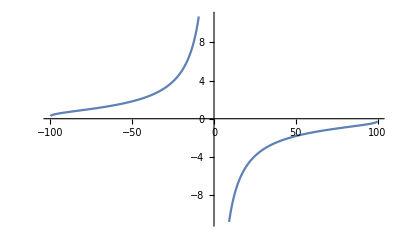

```mathematica
Plot[T[100,U],{U,-99.9,99.9}]
```

```mathematica
Simplify[InvT[N,U]]
```

1/2 (Log[N-U]-Log[N+U])

```mathematica
u=Solve[InvT[N,U]==1/T,U]
```

{{U→-((-1+ⅇ^(2/T)) N)/(1+ⅇ^(2/T))}}

```mathematica
U2[N_,T_]=U/.u[[1]]
```

-((-1+ⅇ^(2/T)) N)/(1+ⅇ^(2/T))

```mathematica
U2[N,T]
```

-((-1+ⅇ^(2/T)) N)/(1+ⅇ^(2/T))

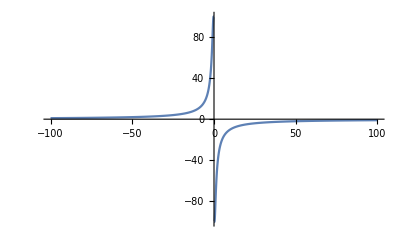

```mathematica
Plot[U2[100,T],{T,-100,100},PlotRange->Full]
```

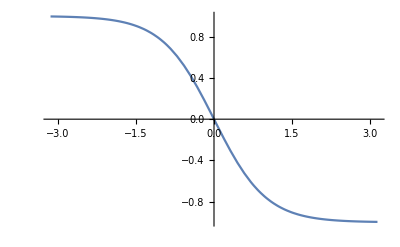

```mathematica
Plot[-Tanh[x],{x,-π,π}]
```

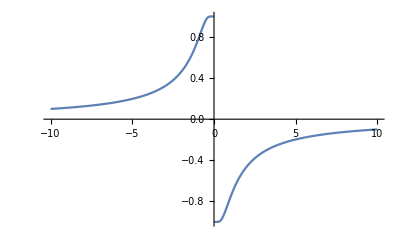

```mathematica
Plot[-Tanh[1/T],{T,-10,10}]
```

```mathematica
CB[N_,T_]:=D[U2[N,T],T]
```

```mathematica
CB[U,T]
```